# Karol Peszek - sprawdzian

Zadanie 1.

```mathematica
(*definicja funkcji*)
ClearAll["Global`*"]
f[x_] := (x^3 + 6x^2 + x + 3) / (x^2 - 1);
```

```mathematica
(*wyznaczanie dziedziny f*)
FunctionDomain[f[x], x, Reals]
```

x<-1||-1<x<1||x>1

```mathematica
(*wyznaczanie asymptot, sprawdzam granice w nieskończonościach i w punktach nieciągłości*)
Limit[f[x] / x, x->Infinity]
```

1

```mathematica
(*asymptota w +Inf*)
```

```mathematica
aPosInf = Limit[f[x] / x, x->Infinity]
```

1

```mathematica
bPosInf = Limit[f[x] - aPosInf* x, x -> Infinity]
```

6

```mathematica
(*zatem w +Inf asymptota ma postać y = x + 6*)
```

```mathematica
(*asymptota w -Inf*)
aNegInf = Limit[f[x] / x, x->-Infinity]
```

1

```mathematica
bNegInf = Limit[f[x] - aNegInf * x, x -> -Infinity]
```

6

```mathematica
(*zatem asymptota w -Inf ma postać y = x + 6*)
```

```mathematica
(*asymptoty pionowe w punktach nieciągłości*)
Limit[f[x], x -> 1, Direction->"FromAbove"]
```

∞

```mathematica
Limit[f[x], x -> 1, Direction->"FromBelow"]
```

-∞

```mathematica
Limit[f[x], x -> -1, Direction->"FromAbove"]
```

-∞

```mathematica
Limit[f[x], x -> -1, Direction->"FromBelow"]
```

∞

```mathematica
(*widzimy również granice prawo i lewostronne w punktach nieciągłości*)
```

```mathematica
(*wyznaczanie miejsc zerowych*)
NSolve[f[x] == 0, x, Reals]
```

{{x→-5.91668}}

```mathematica
(*ekstrema*)
x /. NSolve[f'[x] == 0, x, Reals]
```

{-0.0562583,3.13685}

```mathematica
(*punkty przegięcia*)
x /. NSolve[f''[x] == 0, x, Reals]
```

{-13.2999}

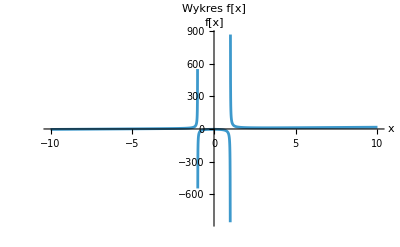

```mathematica
(*rysowanie na wykresie*)
Plot[f[x], {x, -10, 10},
 PlotLabel -> "Wykres f[x]", 
 AxesLabel -> {"x", "f[x]"},
 PlotRange -> All
]
```

Zadanie 2.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*definicja punktów jako liczby zespolone*)
zA = -2 - I;
zB = 1 + 2 I;
```

```mathematica
(*definicja ogólna punktu jako liczby zespolonej*)
z = x + I * y;
```

```mathematica
(*punkt odległy od zA i zB o 1 czyli przecięcie odpowiednich okręgów*)
eqOkragA = Abs[z - zA] == 1;
eqOkragB = Abs[z - zB] == 1;
```

```mathematica
(*równanie elpisy, czyli zbioru punktór których sumaryczna odległość od zA i zB wynosi 7*)
eqElipsa = Abs[z - zA] + Abs[z - zB] == 7;
```

```mathematica
(*równanie hiperboli czyli zbioru punktów których moduł różnicy odległości od zA i zB wynosi 2*)
eqHiperbola = Abs[Abs[z - zA] - Abs[z - zB]] == 2;
```

```mathematica
(*wyświetlanie równań*)
```

```mathematica
Print["Równanie okręgu A: ", ComplexExpand[eqOkragA]]
Print["Równanie okręgu B: ", ComplexExpand[eqOkragB]]
```

Równanie okręgu A: √((2+x)^2+(1+y)^2)==1

Równanie okręgu B: √((-1+x)^2+(-2+y)^2)==1

```mathematica
Print["Równanie elipsy: ", ComplexExpand[eqElipsa]]
```

Równanie elipsy: √((-1+x)^2+(-2+y)^2)+√((2+x)^2+(1+y)^2)==7

```mathematica
Print["Równanie hiperboli: ", ComplexExpand[eqHiperbola]]
```

Równanie hiperboli: √((-Abs[(-1-2 ⅈ)+x+ⅈ y]+Abs[(2+ⅈ)+x+ⅈ y])^2)==2

```mathematica
(*rysowanie wykresu*)
```

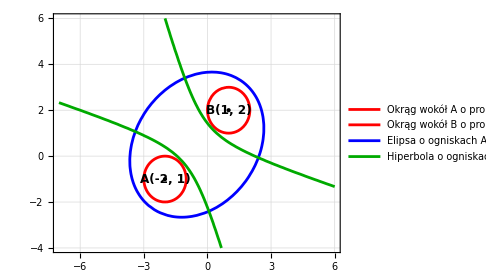

```mathematica
ContourPlot[
 Evaluate[{eqOkragA, eqOkragB, eqElipsa, eqHiperbola}],
 {x, -7, 6}, {y, -4, 6},
 ContourStyle -> {Red, Red, Blue, Darker[Green]},
 
 PlotLegends -> Placed[{
    "Okrąg wokół A o promieniu 1", 
    "Okrąg wokół B o promieniu 1", 
    "Elipsa o ogniskach A i B i sumie odległości 7", 
    "Hiperbola o ogniskach A i B i module różnicy odległości równym 2"
   }, After],
 Epilog -> {
   PointSize[Large], Black,
   Point[{{Re[zA], Im[zA]}, {Re[zB], Im[zB]}}],
   Text[Style["A(-2, 1)", 12, Bold, Background -> White], {Re[zA], Im[zA]}, {0, -2}],
   Text[Style["B(1, 2)", 12, Bold, Background -> White], {Re[zB], Im[zB]}, {0, -2}]
 },
AspectRatio->Automatic,
 GridLines -> Automatic,
 ImageSize -> Medium
]
```

Zadanie 3.

```mathematica
ClearAll["Global`*"]
```

```mathematica
(*gęstość*)
rho[x_, y_, z_] := x^2 + y^2 + z^2;
```

```mathematica
region = ImplicitRegion[
   (x/2)^2 + (y/3)^2 + z^2 <= 1 && !((x - 1)^2 + (y - 1)^2 + z^2 <= 1) &&  x ∈ Reals && y ∈ Reals && z ∈ Reals, 
   {x, y, z}
]
```

ImplicitRegion[x^2/4+y^2/9+z^2≤1&&(-1+x)^2+(-1+y)^2+z^2>1&&x∈ℝ&&y∈ℝ&&z∈ℝ,{x,y,z}]

```mathematica
(*obliczanie objętości*)
V = NIntegrate[1, {x, y, z} ∈ region];
```

```mathematica
(*obliczanie masy*)
M = NIntegrate[rho[x, y, z], {x, y, z} ∈ region];
```

```mathematica
(*momenty statyczne*)
 MxStat =NIntegrate[x * rho[x, y, z], {x, y, z} ∈ region];

MyStat = NIntegrate[y * rho[x, y, z], {x, y, z} ∈ region];
MzStat = NIntegrate[z * rho[x, y, z], {x, y, z} ∈ region];
```

```mathematica
(*moment bezwładności*)
Ix = NIntegrate[rho[x, y, z] *( y^2 + z^2),  {x, y, z} ∈ region];
```

```mathematica
(*obliczanie środka masty*)
CenterOfMass = {MxStat/M, MyStat/M, MzStat/M};
```

```mathematica
(*końcowe wyniki*)
Print["Objętość: ", V];
Print["Środek masy (x, y, z): ", CenterOfMass];
Print["Moment bezwładności względem osi x (Ix): ", Ix];
```

Objętość: 21.5692

Środek masy (x, y, z): {-0.143625+6.45308×10^-25 ⅈ,-0.154714-9.10989×10^-26 ⅈ,0.}

Moment bezwładności względem osi x (Ix): 204.288

Zadanie 4.

```mathematica
ClearAll["Global`*"]
(*definicja a i równania*)
a = 1;
rownanie = x^2 * y''[x] + x * y'[x] + (x^2 - a^2) * y[x] == 0;
```

```mathematica
(*warunki początkowe*)
warunki = {y[0] == 0, y'[0] == 1/2};
```

```mathematica
(*rozwiązanie*)
rozwiazanie = DSolve[{rownanie, warunki}, y[x], x];
```

```mathematica
Print["Rozwiązanie analityczne y(x):"];
Print[y[x] /. rozwiazanie];
```

Rozwiązanie analityczne y(x):

{BesselJ[1,x]}

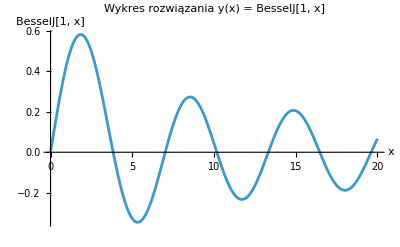

```mathematica
(*rysowanie na wykresie*)
Plot[Evaluate[y[x] /. rozwiazanie], {x, 0, 20},
 PlotLabel -> "Wykres rozwiązania y(x) = BesselJ[1, x]", 
 AxesLabel -> {"x", "BesselJ[1, x]"},
 PlotRange -> All
]
```

Zadanie 5.

```mathematica
ClearAll["Global`*"]
(*definicja stałych i równań*)
sigma = 10;
rho = 28;
beta = 8/3;
```

```mathematica
ukladRownan = {
  x'[t] == sigma * (y[t] - x[t]),
  y'[t] == x[t] * (rho - z[t]) - y[t],
  z'[t] == x[t] * y[t] - beta * z[t]
};
```

```mathematica
(*warunki początkowe*)
warunkiPoczatkowe = {
  x[0] == 1, 
  y[0] == 1, 
  z[0] == 1
};
```

```mathematica
(*rozwiązanie układu równań*)
```

```mathematica
rozwiazanie = NDSolve[
   Join[ukladRownan, warunkiPoczatkowe], 
   {x, y, z}, 
   {t, 0, 50}
];
```

```mathematica
(*rysowanie rozwiązania na wykresie*)
ParametricPlot3D[
  {x[t], y[t], z[t]} /. rozwiazanie,
  {t, 0, 50},
  PlotRange -> All,
  AxesLabel -> {"x", "y", "z"},
  ImageSize -> Medium
]
```

-Graphics3D-